Mathematica file for Electrodynamics course 1FA257
Author: Pietro Longhi

## Project

Fill in the sections below, you can copy-paste cells from the previous sections of this file, and change them as needed.

### 1. Field and potential of a charge distribution

Consider the following charge distribution

```mathematica
rho[{x_,y_}]:=(ⅇ^(1/10 (-(-1+x)^2-y^2)) ((-1+x)^4+y^4))/(((-1+x)^2+y^2)^2)-(ⅇ^(1/10 (-(1+x)^2-y^2)) ((1+x)^4+y^4))/(((1+x)^2+y^2)^2)
```

a. Solve the Poisson equation to obtain the potential.
b. Take the gradient to obtain the electric field
c. Plot both the potential and the electric field

a)

```mathematica
charge=NIntegrate[rho[{x,y}],{x,-∞,∞},{y,-∞,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {1.,8.43766×10^-6}. NIntegrate obtained -8.25728×10^-16 and 3.72154×10^-9 for the integral and error estimates.

-8.25728×10^-16

```mathematica
ϵ0=1;
PoissonEq=D[Phi[x,y],{x,2}]+D[Phi[x,y],{y,2}]==-rho[{x,y}]/ϵ0
```

Phi^(0,2)[x,y]+Phi^(2,0)[x,y]==-(ⅇ^(1/10 (-(-1+x)^2-y^2)) ((-1+x)^4+y^4))/(((-1+x)^2+y^2)^2)+(ⅇ^(1/10 (-(1+x)^2-y^2)) ((1+x)^4+y^4))/(((1+x)^2+y^2)^2)

```mathematica
L1=50;
DirichletBC[x_,y_]:=Phi[x,-L1]==1/(4π ϵ0)charge/((x^2+L1^2)^(1/2))&&Phi[x,L1]==charge/((x^2+L1^2)^(1/2))&&Phi[-L1,y]==charge/((y^2+L1^2)^(1/2))&&Phi[L1,y]==charge/((y^2+L1^2)^(1/2))
sol=NDSolve[PoissonEq&&DirichletBC[x,y],Phi,{x,-L1,L1},{y,-L1,L1}]
Potential[{x_,y_}]:=Phi[x,y]/.sol[[1]]
```

{{Phi→InterpolatingFunction[…]}}

b)

```mathematica
EfieldPoisson[{x1_,y1_}]:={-D[Potential[{x,y}],x],-D[Potential[{x,y}],y]}/.{x->x1,y->y1}
```

c)

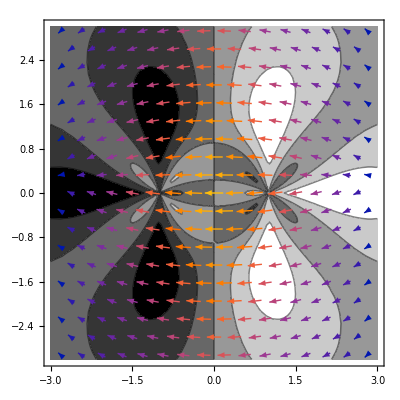

```mathematica
ChargeDistPlot=ContourPlot[rho[{x,y}],{x,-3,3},{y,-3,3},ColorFunction->GrayLevel]
step=0.5;
MeshPts=Table[{x,y},{x,-3,3,step},{y,-3,3,step}];

VectorFieldPoints=Table[Table[
{MeshPts[[i,j]],EfieldPoisson[MeshPts[[i,j]]]}
,{j,1,Length[MeshPts[[i]]]}],{i,1,Length[MeshPts]}];

Show[
ChargeDistPlot,  (*plot the charge distribution*)
ListVectorPlot[VectorFieldPoints,    (*The list of values of the vector field at each point of the mesh*)
VectorScaling->Automatic,Frame->False,PlotRange->{{-3,3},{-3,3}}   (*options for the plot*)
]
,PlotRange->{{-3,3},{-3,3}}
]
```

### 2. Green’s function

Consider the region defined by

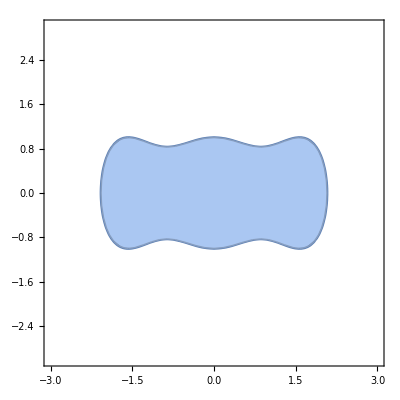

```mathematica
g2[{x_,y_}]:=x^2 Cos[x]^2+y^2-1
S2=ImplicitRegion[g2[{x,y}]==0,{{x, -3,3},{y,-3,3}}];
V2=ImplicitRegion[g2[{x,y}]<=0.001,{{x, -3,3},{y,-3,3}}];
Show[
ContourPlot[g2[{x,y}]==0,{x,-3,3},{y,-3,3}],
Region[V2],
Region[S2]
]
```

a.
Compute the Green function subject to Dirichlet boundary conditions at surface S2. Plot the green’s function at {x,y}={1/2,0} as a function of {x’,y’}

```mathematica
peakfactor=10^3;
Subscript[G1, x_,y_]:=NDSolveValue[{
∇_{x2,y2}^2 f[x2,y2] ==-4π (peakfactor/π E^(-peakfactor((x-x2)^2+(y-y2)^2)))(*Poisson eq., with a Gaussian replacing the 2d Dirac Delta*),
DirichletCondition[f[x2, y2] == 0, True]  (* Dirichlet boundary condition *)
}, f, {x2,y2} ∈V2]
f1=Subscript[G1, 1/2,0];
Plot3D[f1[x,y], {x,y} ∈ V2,PlotRange->All]
```

-Graphics3D-

b. 
Consider the following charge configuration
q_1= 1  {x_1,y_1}={2,1}
q_2= 1  {x_2,y_2}={0,2}
q_3= -2  {x_3,y_3}={-1,-2}
Compute the exact potential using Coulomb’s formula
Apply Green’s theorem with Dirichlet boundary condition to compute the potential at a point inside the region V2, by supplying :
- the charge distribution above
- the boundary values for the potential 
-Graphics-

```mathematica
ϵ0=1;
PhiPoint[q0_,{x0_,y0_}]:=1/(4 π ϵ0)q0/(((x-x0)^2+(y-y0)^2)^(1/2))
ρ[x_,y_]:=DiracDelta[x-2,y-1]+DiracDelta[x,y-2]+DiracDelta[x+1,y+2]
PhiTot=PhiPoint[1,{2,1}]+PhiPoint[1,{0,2}]+PhiPoint[-2,{-1,-2}]
```

1/(4 π √(x^2+(-2+y)^2))+1/(4 π √((-2+x)^2+(-1+y)^2))-1/(2 π √((1+x)^2+(2+y)^2))

```mathematica
f1=Subscript[G1, 0,0];
df1dx=D[f1[x,y],x];
df1dy=D[f1[x,y],y];
df1dn=Normalize[{x,y}]. {df1dx,df1dy};
-1/(4π)NIntegrate[PhiTot df1dn ,{x,y}∈S2]//Quiet
PhiTot/.{x->0,y->0}//N
```

0.00551499

0.00420061

c.
Give the numerical value of the potential obtained from the Green function at the points
{x,y}={0,0}, {1/2,0},{0,1/2},{1/2,1/2}
Also give the value of the true potential (Coulomb’s formula) at each these points

```mathematica
mesh = {{0.0,0.0},{0.5,0.0},{0.0,0.5},{0.5,0.5}}
GreenPhi[{x0_,y0_}]:=1/(4π)NIntegrate[PhiTot Normalize[{x,y}].{D[Subscript[G1, x0,y0][x,y],x],D[Subscript[G1, x0,y0][x,y],y]} ,{x,y}∈S2]//Quiet
TruePhi[{x0_,y0_}]:=PhiTot/.{x->x0,y->y0}
Greenlist=Table[
Append[p,GreenPhi[p]]
,{p,mesh}]
Coulomblist=Table[
Append[p,TruePhi[p]]
,{p,mesh}]
```

{{0.,0.},{0.5,0.},{0.,0.5},{0.5,0.5}}

{{0.,0.,-0.00551499},{0.5,0.,-0.0230307},{0.,0.5,-0.0394259},{0.5,0.5,-0.0487821}}

{{0.,0.,0.00420061},{0.5,0.,0.0190804},{0.,0.5,0.0325437},{0.5,0.5,0.0460687}}

```mathematica
Δlist=Table[
Append[p,GreenPhi[p]-TruePhi[p]]
,{p,mesh}]
ListPlot3D[Δlist,PlotRange->All]
```

{{0.,0.,-0.0097156},{0.5,0.,-0.0421111},{0.,0.5,-0.0719696},{0.5,0.5,-0.0948509}}

-Graphics3D-

### 3. Waveguides

Consider a rectangular waveguide with cross section of size [0,a] x [0,b] in the x, y directions.

a. Plot the values of k_λ/ω_λ for the first five TE modes. Set μ=ϵ=1 for simplicity. 
     Fix (a=1,b=1) then repeat with (a=1.5,b=1). What do you observe?

b. Fix a=1.5 and b=1. Plot the transverse electric field of the lowest five modes.

c. Now introduce time, and plot the behavior of the transverse electric field at z=0 for the (1,0), (0,1) and (1,1) modes as a function ot time (use the function Manipulate[ StramPlot[...] , {t,0,10}]).
    Repeat with the linear superposition of modes (1,0) + (0,1)